```mathematica
Needs["QMB`"]
```

```mathematica
BoseHubbardHilbertSpaceDimension[4,4]
```

35

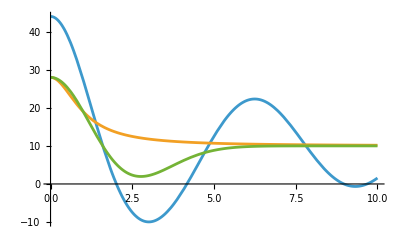

```mathematica
Plot[10+2*9*{Re[1-t Exp[-t^2/π](Erfi[t/√π]+ⅈ)]+8/9*Re[l[t,0.1]],Re[1/(1+ⅈ t)],Re[-1/8 ⅈ (4 t-ⅇ^(-(π t^2)/16) (-8+π t^2) (ⅈ+Erfi[(√π t)/4]))]}//Evaluate,{t,0,10}]
```

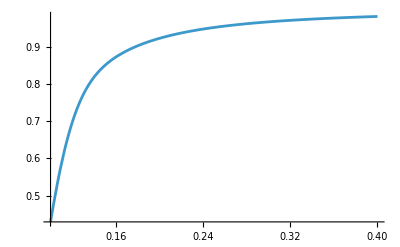

```mathematica
Plot[1+Total[Re[l[25t,#]]&/@Power[1.01,Range[8]]],{t,0.1,0.4},PlotRange->All]
```

```mathematica
Integrate[Exp[-I*s*t]*PsGUE[s],{s,0,Infinity},Assumptions->{t>=0,σ>=0}]
```

-1/8 ⅈ (4 t-ⅇ^(-(π t^2)/16) (-8+π t^2) (ⅈ+Erfi[(√π t)/4]))

```mathematica
PsGUE[s_]:=32/π^2 s^2 Exp[-4/π s^2]
```

```mathematica
Convolve[PDF[RayleighDistribution[Sqrt[2/Pi]],x],PDF[RayleighDistribution[Sqrt[2/Pi]],x],x,y]
```

Piecewise[{{1/16 ⅇ^(-(π y^2)/4) π (4 y+√2 ⅇ^((π y^2)/8) (-4+π y^2) Erf[1/2 √(π/2) y]), y>0}, {0, True}}]

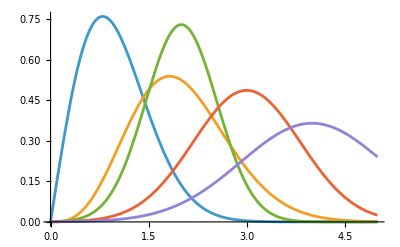

```mathematica
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],y],1/16 ⅇ^(-(π y^2)/4) π (4 y+√2 ⅇ^((π y^2)/8) (-4+π y^2) Erf[1/2 √(π/2) y]),PDF[NormalDistribution[2,2((4-π)/π)],y],PDF[NormalDistribution[3,3((4-π)/π)],y],PDF[NormalDistribution[4,4((4-π)/π)],y]},{y,0,5}]
```

```mathematica
Integrate[y^2*PDF[RayleighDistribution[Sqrt[2/Pi]],y],{y,0,Infinity}]
```

4/π

```mathematica
Integrate[1/16 ⅇ^(-(π y^2)/4) π (4 y+√2 ⅇ^((π y^2)/8) (-4+π y^2) Erf[1/2 √(π/2) y]),{y,0,Infinity}]
Integrate[y*1/16 ⅇ^(-(π y^2)/4) π (4 y+√2 ⅇ^((π y^2)/8) (-4+π y^2) Erf[1/2 √(π/2) y]),{y,0,Infinity}]
Integrate[y^2*1/16 ⅇ^(-(π y^2)/4) π (4 y+√2 ⅇ^((π y^2)/8) (-4+π y^2) Erf[1/2 √(π/2) y]),{y,0,Infinity}]
```

1

2

2+8/π

```mathematica
2+8/π-2^2
```

-2+8/π

```mathematica
(*2 convolutions*)
g2[s_]:=Piecewise[{{(Pi*s)/4*Exp[-(Pi*s^2)/8]*(BesselI[0,(Pi*s^2)/8]+BesselI[1,(Pi*s^2)/8]),s>=0},{0,s<0}}]
(*3 convolutions*)
g[s_]:=Piecewise[{{(Pi^3/64)*s^5*Exp[-(Pi*s^2)/4],s>=0},{0,s<0}}]
```

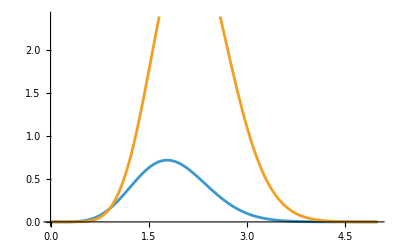

```mathematica
Plot[
{Piecewise[{{(Pi^3/64)*s^5*Exp[-(Pi*s^2)/4],s>=0},{0,s<0}}],
Piecewise[{{(Pi^5/8^3)*s^7*Exp[-(Pi*s^2)/4],s>=0},{0,s<0}}]}
,{s,0,5}]
```

## dg

```mathematica
β=11.;
h[s_,β_]:=s^β*Exp[-s^2]
A=(Integrate[h[s,β],{s,0,Infinity}])^-1;
h[s_,β_]:=A*s^β*Exp[-s^2]
Integrate[h[s,β],{s,0,Infinity}]

c=Integrate[s*h[s,β],{s,0,Infinity}];
h[s_,β_]:=A*(c*s)^β*Exp[-(c*s)^2]*c
Integrate[s*h[s,β],{s,0,Infinity}]
Sqrt[Integrate[s^2*h[s,β],{s,0,Infinity}]-1.]
```

1.

1.

0.206148

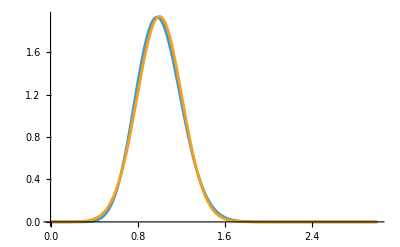

```mathematica
Plot[{h[s,β],PDF[NormalDistribution[1.,0.2061481013924111],s]},{s,0,3},PlotRange->All]
```

```mathematica
(4.-π)/π
```

0.27324

Orden 10

```mathematica
β=36.;
h[s_,β_]:=s^β*Exp[-s^2]
A=(Integrate[h[s,β],{s,0,Infinity}])^-1;
h[s_,β_]:=A*s^β*Exp[-s^2]
Integrate[h[s,β],{s,0,Infinity}]

c=Integrate[s*h[s,β],{s,0,Infinity}];
h[s_,β_]:=A*(c*s)^β*Exp[-(c*s)^2]*c
Integrate[s*h[s,β],{s,0,Infinity}]
std=Sqrt[Integrate[s^2*h[s,β],{s,0,Infinity}]-1.]
```

1.

1.

0.116634

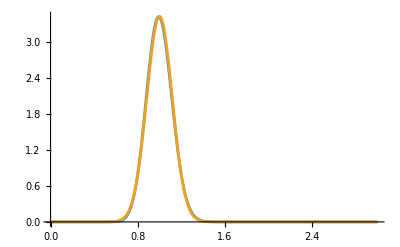

```mathematica
Plot[{h[s,β],PDF[NormalDistribution[1.,std],s]},{s,0,3},PlotRange->All]
```

Orden 15

```mathematica
β=73.;
h[s_,β_]:=s^β*Exp[-s^2]
A=(Integrate[h[s,β],{s,0,Infinity}])^-1;
h[s_,β_]:=A*s^β*Exp[-s^2]
Integrate[h[s,β],{s,0,Infinity}]

c=Integrate[s*h[s,β],{s,0,Infinity}];
h[s_,β_]:=A*(c*s)^β*Exp[-(c*s)^2]*c
Integrate[s*h[s,β],{s,0,Infinity}]
std=Sqrt[Integrate[s^2*h[s,β],{s,0,Infinity}]-1.]
```

1.

1.

0.0823373

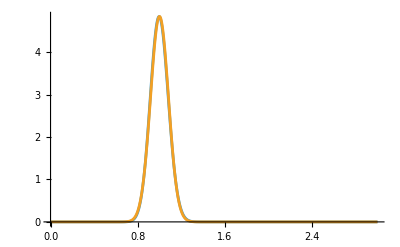

```mathematica
Plot[{h[s,β],PDF[NormalDistribution[1.,std],s]},{s,0,3},PlotRange->All]
```

## Spacings

```mathematica
ClearAll[σ]
```

```mathematica
Integrate[Exp[-I*s*t]*PDF[NormalDistribution[1,σ],s],{s,0,Infinity},Assumptions->{t>=0,σ>=0}]
```

1/2 ⅇ^(-1/2 t (2 ⅈ+t σ^2)) (1+Erf[(1-ⅈ t σ^2)/(√2 σ)])

```mathematica
l[t_,σ_]:=1/2 ⅇ^(-1/2 t (2 ⅈ+t σ^2)) (1+Erf[(1-ⅈ t σ^2)/(√2 σ)])
```

```mathematica
Manipulate[
Plot[Re[l[t,σ]],{t,0.1,5}]
,{σ,0.02,0.1,0.01}]
```

General::munfl: Exp[-1253.57+0.10014 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
ⅇ^(-1/2 t (2 ⅈ+t σ^2))/.{σ->0.01,t->1.}
```

0.540275-0.841429 ⅈ

```mathematica
l[1.,0.01]
```

General::munfl: Exp[-5004.26+1.0001 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

0.540275-0.841429 ⅈ

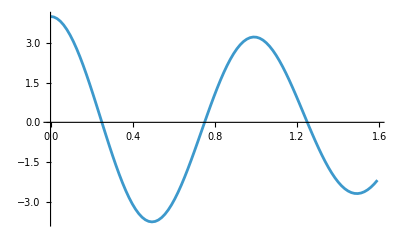

```mathematica
Quiet[ListPlot[Table[{t/(2Pi),Re[l[t,0.1]]+Re[l[t,0.2]]+Re[l[t,0.05]]+Re[l[t,0.02]]},{t,0.,10.,0.1}],Joined->True]]
```

```mathematica
1./2000^2
```

0.0005

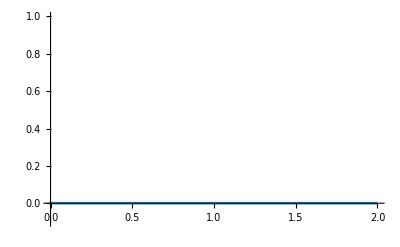

```mathematica
Plot[1/2000^2*Re[Exp[-ⅈ 30.*t]],{t,0,2},PlotRange->{All,{-0.1,1}}]
```